```mathematica
SetDirectory["/Volumes/MicroSD/PostDoc_SD/ZrC/Defect_annealed/DOS"];
file={"DOS_all"};
dosAll=ReadList[file[[1]],{Number, Number}];
labeldos={"4575","4.625","4.6583","4.685","4.6910 (Exp.)","4730","4759","4801","4850"}
```

{4575,4.625,4.6583,4.685,4.6910 (Exp.),4730,4759,4801,4850}

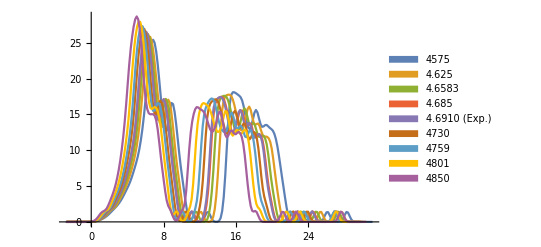

```mathematica
ListPlot[Table[Partition[dosAll,201][[i]],{i,1,9}],PlotLegends->SwatchLegend[labeldos],Joined->True]
```

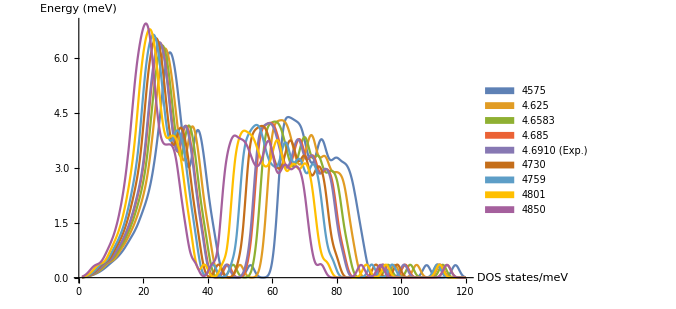

```mathematica
DOSfits=Table[Interpolation[Partition[dosAll,201][[i]]],{i,1,9}];
Plot[Evaluate@Table[(1/4.135665538536)*DOSfits[[i]][x/4.135665538536],{i,1,9}],{x,1,120},PlotLegends->SwatchLegend[labeldos],PlotStyle->Thick,ImageSize->500,AxesLabel->{"DOS\n states/meV","Energy (meV)"}]
```

```mathematica
SetDirectory["/Volumes/MicroSD/PostDoc_SD/ZrC/ZrC_QHA_output"];
qhaDefect={"QHA_defect/e-v.dat","QHA_defect/volume_expansion.dat","QHA_defect/volume-temperature.dat","QHA_defect/gruneisen-temperature.dat","QHA_defect/gibbs-temperature.dat","QHA_defect/bulk_modulus-temperature.dat","QHA_defect/Cp-temperature.dat","QHA_defect/dsdv-temperature.dat"};
qhaNormal={"QHA_normal/e-v.dat","QHA_normal/volume_expansion.dat","QHA_normal/volume-temperature.dat","QHA_normal/gruneisen-temperature.dat","QHA_normal/gibbs-temperature.dat","QHA_normal/bulk_modulus-temperature.dat","QHA_normal/Cp-temperature.dat","QHA_normal/dsdv-temperature.dat"};
swatch={PlotLegends->SwatchLegend[{"Defective","Perfect"},left],ImageSize->400,Joined->True,PlotStyle->{Thick}};
defect=Table[ReadList[qhaDefect[[i]],{Number, Number}],{i,1,8}];
normal=Table[ReadList[qhaNormal[[i]],{Number, Number}],{i,1,8}];
```

```mathematica
normal[[1]]
```

{{766.060875,-673.839},{808.515666496,-675.71},{843.908625,-674.609},{884.736,-670.996},{926.859375,-665.213}}

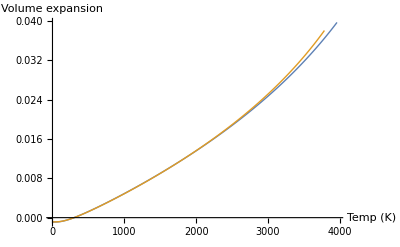

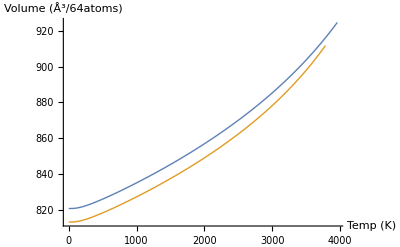

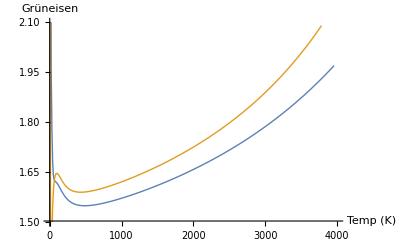

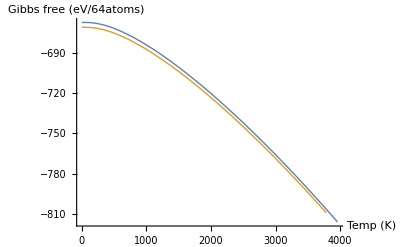

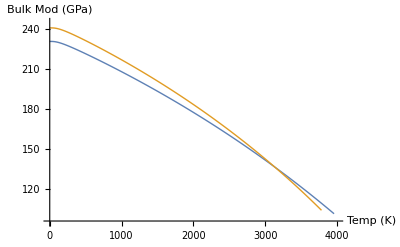

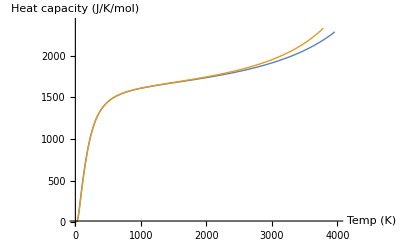

```mathematica
(*Volume expansion*)
a=ListPlot[{defect[[2]],normal[[2]]},Evaluate@swatch,AxesLabel->{"Temp\n(K)","Volume\n expansion"}]
(*Volume-Temperature*)
b=ListPlot[{defect[[3]],normal[[3]]},Evaluate@swatch,AxesLabel->{"Temp\n(K)","Volume\n(Å^3/64atoms)"}]
(*Gruneisen-Temperature*)
c=ListPlot[{defect[[4]],normal[[4]]},PlotRange->{{0,4000},{1.5,2.1}},Evaluate@swatch,AxesLabel->{"Temp\n(K)","Grüneisen"}]
(*Gibbs-Temperature*)
d=ListPlot[{defect[[5]],normal[[5]]},Evaluate@swatch,AxesLabel->{"Temp\n(K)","Gibbs free\n(eV/64atoms)"},PlotRange->{{0,4000},{-660,-820}}]
(*Bulkmod-Temperature*)
e=ListPlot[{defect[[6]],normal[[6]]},Evaluate@swatch,PlotRange->{{0,4000},{95,245}},AxesLabel->{"Temp\n(K)","Bulk Mod\n(GPa)"}]
(*Cp-Temperature*)
f=ListPlot[{defect[[7]],normal[[7]]},PlotRange->{{0,4000},{1,2400}},Evaluate@swatch,AxesLabel->{"Temp\n(K)","Heat capacity\n(J/K/mol)"}]
```

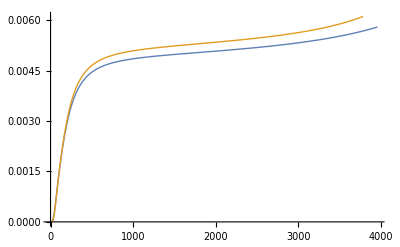

```mathematica
(*dSdV-Temperature*)
g=ListPlot[{defect[[8]],normal[[8]]},Evaluate@swatch]
```

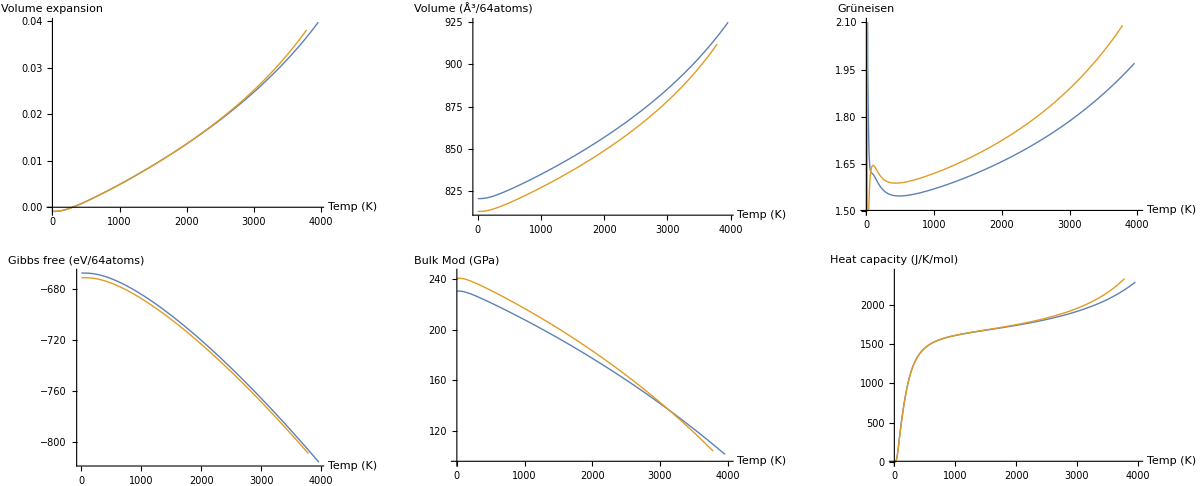

```mathematica
GraphicsGrid[{{a,b,c},{d,e,f}},ImageSize->1200]
```

```mathematica
{defect[[2]],normal[[2]]}
```

{{{0.,-0.000888566},{10.,-0.000888562},{20.,-0.000888451},{30.,-0.000887894},{40.,-0.000886226},{50.,-0.000882583},{60.,-0.000876272},{70.,-0.000866931},{80.,-0.000854464},{90.,-0.000838916},{100.,-0.000820393},{110.,-0.000799015},{120.,-0.000774904},{130.,-0.000748177},{140.,-0.000718951},{150.,-0.000687338},{160.,-0.000653455},{170.,-0.000617415},{180.,-0.000579332},{190.,-0.000539319},{200.,-0.000497485},{210.,-0.000453937},{220.,-0.000408776},{230.,-0.0003621},{240.,-0.000314},{250.,-0.000264563},{260.,-0.000213872},{270.,-0.000162001},{280.,-0.000109022},{290.,-0.0000550014},{300.,0.},{310.,0.0000559251},{320.,0.000112721},{330.,0.000170339},{340.,0.000228733},{350.,0.000287862},{360.,0.000347686},{370.,0.000408171},{380.,0.000469281},{390.,0.000530987},{400.,0.000593261},{410.,0.000656074},{420.,0.000719403},{430.,0.000783225},{440.,0.000847519},{450.,0.000912264},{460.,0.000977443},{470.,0.00104304},{480.,0.00110903},{490.,0.00117542},{500.,0.00124217},{510.,0.00130928},{520.,0.00137674},{530.,0.00144453},{540.,0.00151265},{550.,0.00158109},{560.,0.00164983},{570.,0.00171886},{580.,0.00178819},{590.,0.0018578},{600.,0.00192768},{610.,0.00199783},{620.,0.00206824},{630.,0.00213891},{640.,0.00220982},{650.,0.00228099},{660.,0.00235239},{670.,0.00242402},{680.,0.00249589},{690.,0.00256799},{700.,0.0026403},{710.,0.00271284},{720.,0.0027856},{730.,0.00285856},{740.,0.00293174},{750.,0.00300512},{760.,0.00307871},{770.,0.0031525},{780.,0.00322649},{790.,0.00330068},{800.,0.00337506},{810.,0.00344963},{820.,0.0035244},{830.,0.00359936},{840.,0.0036745},{850.,0.00374983},{860.,0.00382535},{870.,0.00390104},{880.,0.00397693},{890.,0.00405299},{900.,0.00412923},{910.,0.00420565},{920.,0.00428225},{930.,0.00435903},{940.,0.00443599},{950.,0.00451312},{960.,0.00459042},{970.,0.0046679},{980.,0.00474555},{990.,0.00482338},{1000.,0.00490138},{1010.,0.00497955},{1020.,0.00505789},{1030.,0.0051364},{1040.,0.00521509},{1050.,0.00529394},{1060.,0.00537297},{1070.,0.00545216},{1080.,0.00553153},{1090.,0.00561106},{1100.,0.00569077},{1110.,0.00577065},{1120.,0.00585069},{1130.,0.00593091},{1140.,0.00601129},{1150.,0.00609185},{1160.,0.00617257},{1170.,0.00625347},{1180.,0.00633453},{1190.,0.00641576},{1200.,0.00649717},{1210.,0.00657874},{1220.,0.00666049},{1230.,0.00674241},{1240.,0.00682449},{1250.,0.00690675},{1260.,0.00698918},{1270.,0.00707179},{1280.,0.00715456},{1290.,0.00723751},{1300.,0.00732063},{1310.,0.00740392},{1320.,0.00748739},{1330.,0.00757103},{1340.,0.00765485},{1350.,0.00773884},{1360.,0.00782301},{1370.,0.00790735},{1380.,0.00799187},{1390.,0.00807656},{1400.,0.00816143},{1410.,0.00824649},{1420.,0.00833172},{1430.,0.00841712},{1440.,0.00850271},{1450.,0.00858848},{1460.,0.00867443},{1470.,0.00876056},{1480.,0.00884687},{1490.,0.00893337},{1500.,0.00902004},{1510.,0.00910691},{1520.,0.00919395},{1530.,0.00928118},{1540.,0.0093686},{1550.,0.00945621},{1560.,0.009544},{1570.,0.00963198},{1580.,0.00972015},{1590.,0.0098085},{1600.,0.00989705},{1610.,0.00998579},{1620.,0.0100747},{1630.,0.0101638},{1640.,0.0102532},{1650.,0.0103427},{1660.,0.0104324},{1670.,0.0105223},{1680.,0.0106124},{1690.,0.0107027},{1700.,0.0107932},{1710.,0.0108839},{1720.,0.0109748},{1730.,0.0110659},{1740.,0.0111572},{1750.,0.0112487},{1760.,0.0113404},{1770.,0.0114323},{1780.,0.0115244},{1790.,0.0116167},{1800.,0.0117093},{1810.,0.011802},{1820.,0.0118949},{1830.,0.0119881},{1840.,0.0120815},{1850.,0.0121751},{1860.,0.0122689},{1870.,0.0123629},{1880.,0.0124571},{1890.,0.0125515},{1900.,0.0126462},{1910.,0.0127411},{1920.,0.0128362},{1930.,0.0129315},{1940.,0.0130271},{1950.,0.0131229},{1960.,0.0132188},{1970.,0.0133151},{1980.,0.0134115},{1990.,0.0135082},{2000.,0.0136051},{2010.,0.0137023},{2020.,0.0137996},{2030.,0.0138972},{2040.,0.0139951},{2050.,0.0140931},{2060.,0.0141915},{2070.,0.01429},{2080.,0.0143888},{2090.,0.0144878},{2100.,0.0145871},{2110.,0.0146866},{2120.,0.0147864},{2130.,0.0148864},{2140.,0.0149867},{2150.,0.0150872},{2160.,0.0151879},{2170.,0.0152889},{2180.,0.0153902},{2190.,0.0154917},{2200.,0.0155935},{2210.,0.0156955},{2220.,0.0157978},{2230.,0.0159004},{2240.,0.0160032},{2250.,0.0161062},{2260.,0.0162096},{2270.,0.0163132},{2280.,0.0164171},{2290.,0.0165212},{2300.,0.0166256},{2310.,0.0167303},{2320.,0.0168353},{2330.,0.0169405},{2340.,0.0170461},{2350.,0.0171519},{2360.,0.0172579},{2370.,0.0173643},{2380.,0.017471},{2390.,0.0175779},{2400.,0.0176851},{2410.,0.0177926},{2420.,0.0179005},{2430.,0.0180086},{2440.,0.018117},{2450.,0.0182256},{2460.,0.0183346},{2470.,0.0184439},{2480.,0.0185535},{2490.,0.0186634},{2500.,0.0187736},{2510.,0.0188842},{2520.,0.018995},{2530.,0.0191061},{2540.,0.0192176},{2550.,0.0193294},{2560.,0.0194414},{2570.,0.0195539},{2580.,0.0196666},{2590.,0.0197797},{2600.,0.019893},{2610.,0.0200068},{2620.,0.0201208},{2630.,0.0202352},{2640.,0.0203499},{2650.,0.020465},{2660.,0.0205804},{2670.,0.0206961},{2680.,0.0208122},{2690.,0.0209286},{2700.,0.0210454},{2710.,0.0211625},{2720.,0.02128},{2730.,0.0213978},{2740.,0.021516},{2750.,0.0216346},{2760.,0.0217535},{2770.,0.0218728},{2780.,0.0219925},{2790.,0.0221125},{2800.,0.0222329},{2810.,0.0223537},{2820.,0.0224749},{2830.,0.0225964},{2840.,0.0227184},{2850.,0.0228407},{2860.,0.0229634},{2870.,0.0230865},{2880.,0.02321},{2890.,0.0233339},{2900.,0.0234582},{2910.,0.0235829},{2920.,0.023708},{2930.,0.0238335},{2940.,0.0239595},{2950.,0.0240858},{2960.,0.0242126},{2970.,0.0243398},{2980.,0.0244674},{2990.,0.0245954},{3000.,0.0247239},{3010.,0.0248528},{3020.,0.0249822},{3030.,0.025112},{3040.,0.0252422},{3050.,0.0253729},{3060.,0.025504},{3070.,0.0256356},{3080.,0.0257677},{3090.,0.0259002},{3100.,0.0260332},{3110.,0.0261666},{3120.,0.0263006},{3130.,0.026435},{3140.,0.0265698},{3150.,0.0267052},{3160.,0.0268411},{3170.,0.0269774},{3180.,0.0271143},{3190.,0.0272516},{3200.,0.0273894},{3210.,0.0275278},{3220.,0.0276667},{3230.,0.027806},{3240.,0.0279459},{3250.,0.0280864},{3260.,0.0282273},{3270.,0.0283688},{3280.,0.0285108},{3290.,0.0286534},{3300.,0.0287965},{3310.,0.0289402},{3320.,0.0290844},{3330.,0.0292292},{3340.,0.0293745},{3350.,0.0295204},{3360.,0.0296669},{3370.,0.0298139},{3380.,0.0299616},{3390.,0.0301098},{3400.,0.0302587},{3410.,0.0304081},{3420.,0.0305581},{3430.,0.0307088},{3440.,0.03086},{3450.,0.0310119},{3460.,0.0311644},{3470.,0.0313175},{3480.,0.0314713},{3490.,0.0316257},{3500.,0.0317808},{3510.,0.0319365},{3520.,0.0320928},{3530.,0.0322499},{3540.,0.0324076},{3550.,0.032566},{3560.,0.032725},{3570.,0.0328848},{3580.,0.0330452},{3590.,0.0332064},{3600.,0.0333683},{3610.,0.0335308},{3620.,0.0336942},{3630.,0.0338582},{3640.,0.034023},{3650.,0.0341885},{3660.,0.0343547},{3670.,0.0345217},{3680.,0.0346895},{3690.,0.0348581},{3700.,0.0350274},{3710.,0.0351975},{3720.,0.0353684},{3730.,0.0355402},{3740.,0.0357127},{3750.,0.035886},{3760.,0.0360602},{3770.,0.0362352},{3780.,0.036411},{3790.,0.0365877},{3800.,0.0367653},{3810.,0.0369437},{3820.,0.037123},{3830.,0.0373032},{3840.,0.0374843},{3850.,0.0376663},{3860.,0.0378492},{3870.,0.038033},{3880.,0.0382177},{3890.,0.0384034},{3900.,0.0385901},{3910.,0.0387777},{3920.,0.0389662},{3930.,0.0391558},{3940.,0.0393464},{3950.,0.0395379},{3960.,0.0397305}},{{0.,-0.000861634},{5.,-0.000861634},{10.,-0.00086163},{15.,-0.000861612},{20.,-0.00086156},{25.,-0.000861439},{30.,-0.000861191},{35.,-0.000860732},{40.,-0.000859955},{45.,-0.000858747},{50.,-0.000857004},{55.,-0.000854642},{60.,-0.000851596},{65.,-0.000847823},{70.,-0.000843299},{75.,-0.000838012},{80.,-0.000831961},{85.,-0.000825153},{90.,-0.000817595},{95.,-0.0008093},{100.,-0.000800282},{105.,-0.000790554},{110.,-0.000780129},{115.,-0.000769021},{120.,-0.000757245},{125.,-0.000744813},{130.,-0.000731738},{135.,-0.000718034},{140.,-0.000703715},{145.,-0.000688794},{150.,-0.000673285},{155.,-0.000657201},{160.,-0.000640557},{165.,-0.000623366},{170.,-0.000605642},{175.,-0.0005874},{180.,-0.000568652},{185.,-0.000549414},{190.,-0.000529698},{195.,-0.000509519},{200.,-0.000488889},{205.,-0.000467822},{210.,-0.000446332},{215.,-0.00042443},{220.,-0.000402129},{225.,-0.000379442},{230.,-0.000356379},{235.,-0.000332954},{240.,-0.000309176},{245.,-0.000285057},{250.,-0.000260607},{255.,-0.000235836},{260.,-0.000210755},{265.,-0.000185373},{270.,-0.000159698},{275.,-0.000133741},{280.,-0.000107509},{285.,-0.0000810116},{290.,-0.0000542557},{295.,-0.0000272493},{300.,0.},{305.,0.0000274852},{310.,0.0000551994},{315.,0.0000831358},{320.,0.000111288},{325.,0.000139651},{330.,0.000168217},{335.,0.000196982},{340.,0.000225939},{345.,0.000255084},{350.,0.000284411},{355.,0.000313916},{360.,0.000343594},{365.,0.00037344},{370.,0.00040345},{375.,0.00043362},{380.,0.000463946},{385.,0.000494424},{390.,0.00052505},{395.,0.000555821},{400.,0.000586733},{405.,0.000617783},{410.,0.000648968},{415.,0.000680284},{420.,0.000711729},{425.,0.0007433},{430.,0.000774994},{435.,0.000806809},{440.,0.000838741},{445.,0.000870788},{450.,0.000902948},{455.,0.00093522},{460.,0.000967599},{465.,0.00100009},{470.,0.00103268},{475.,0.00106537},{480.,0.00109816},{485.,0.00113105},{490.,0.00116404},{495.,0.00119712},{500.,0.0012303},{505.,0.00126357},{510.,0.00129693},{515.,0.00133037},{520.,0.00136391},{525.,0.00139753},{530.,0.00143123},{535.,0.00146502},{540.,0.00149889},{545.,0.00153284},{550.,0.00156687},{555.,0.00160098},{560.,0.00163516},{565.,0.00166942},{570.,0.00170376},{575.,0.00173817},{580.,0.00177265},{585.,0.00180721},{590.,0.00184183},{595.,0.00187653},{600.,0.0019113},{605.,0.00194613},{610.,0.00198104},{615.,0.00201601},{620.,0.00205104},{625.,0.00208615},{630.,0.00212131},{635.,0.00215655},{640.,0.00219184},{645.,0.0022272},{650.,0.00226262},{655.,0.0022981},{660.,0.00233364},{665.,0.00236925},{670.,0.00240491},{675.,0.00244063},{680.,0.00247642},{685.,0.00251226},{690.,0.00254816},{695.,0.00258411},{700.,0.00262013},{705.,0.00265619},{710.,0.00269232},{715.,0.0027285},{720.,0.00276474},{725.,0.00280103},{730.,0.00283738},{735.,0.00287378},{740.,0.00291023},{745.,0.00294674},{750.,0.0029833},{755.,0.00301992},{760.,0.00305658},{765.,0.0030933},{770.,0.00313007},{775.,0.0031669},{780.,0.00320377},{785.,0.0032407},{790.,0.00327767},{795.,0.0033147},{800.,0.00335178},{805.,0.0033889},{810.,0.00342608},{815.,0.00346331},{820.,0.00350058},{825.,0.00353791},{830.,0.00357528},{835.,0.00361271},{840.,0.00365018},{845.,0.0036877},{850.,0.00372527},{855.,0.00376288},{860.,0.00380055},{865.,0.00383826},{870.,0.00387602},{875.,0.00391383},{880.,0.00395169},{885.,0.00398959},{890.,0.00402754},{895.,0.00406554},{900.,0.00410358},{905.,0.00414167},{910.,0.00417981},{915.,0.00421799},{920.,0.00425622},{925.,0.0042945},{930.,0.00433282},{935.,0.00437119},{940.,0.0044096},{945.,0.00444807},{950.,0.00448657},{955.,0.00452512},{960.,0.00456372},{965.,0.00460237},{970.,0.00464106},{975.,0.00467979},{980.,0.00471857},{985.,0.0047574},{990.,0.00479627},{995.,0.00483519},{1000.,0.00487415},{1005.,0.00491316},{1010.,0.00495221},{1015.,0.00499131},{1020.,0.00503045},{1025.,0.00506964},{1030.,0.00510887},{1035.,0.00514815},{1040.,0.00518747},{1045.,0.00522684},{1050.,0.00526626},{1055.,0.00530571},{1060.,0.00534522},{1065.,0.00538476},{1070.,0.00542436},{1075.,0.005464},{1080.,0.00550368},{1085.,0.00554341},{1090.,0.00558318},{1095.,0.005623},{1100.,0.00566286},{1105.,0.00570277},{1110.,0.00574272},{1115.,0.00578272},{1120.,0.00582276},{1125.,0.00586285},{1130.,0.00590298},{1135.,0.00594315},{1140.,0.00598338},{1145.,0.00602364},{1150.,0.00606396},{1155.,0.00610431},{1160.,0.00614472},{1165.,0.00618516},{1170.,0.00622566},{1175.,0.00626619},{1180.,0.00630678},{1185.,0.0063474},{1190.,0.00638808},{1195.,0.0064288},{1200.,0.00646956},{1205.,0.00651037},{1210.,0.00655122},{1215.,0.00659213},{1220.,0.00663307},{1225.,0.00667406},{1230.,0.0067151},{1235.,0.00675618},{1240.,0.00679731},{1245.,0.00683848},{1250.,0.00687971},{1255.,0.00692097},{1260.,0.00696228},{1265.,0.00700364},{1270.,0.00704504},{1275.,0.00708649},{1280.,0.00712799},{1285.,0.00716953},{1290.,0.00721112},{1295.,0.00725276},{1300.,0.00729444},{1305.,0.00733617},{1310.,0.00737794},{1315.,0.00741976},{1320.,0.00746163},{1325.,0.00750354},{1330.,0.0075455},{1335.,0.00758751},{1340.,0.00762957},{1345.,0.00767167},{1350.,0.00771382},{1355.,0.00775601},{1360.,0.00779826},{1365.,0.00784055},{1370.,0.00788289},{1375.,0.00792527},{1380.,0.00796771},{1385.,0.00801019},{1390.,0.00805272},{1395.,0.00809529},{1400.,0.00813792},{1405.,0.00818059},{1410.,0.00822331},{1415.,0.00826608},{1420.,0.0083089},{1425.,0.00835176},{1430.,0.00839467},{1435.,0.00843764},{1440.,0.00848065},{1445.,0.00852371},{1450.,0.00856682},{1455.,0.00860997},{1460.,0.00865318},{1465.,0.00869644},{1470.,0.00873974},{1475.,0.0087831},{1480.,0.0088265},{1485.,0.00886995},{1490.,0.00891346},{1495.,0.00895701},{1500.,0.00900061},{1505.,0.00904427},{1510.,0.00908797},{1515.,0.00913172},{1520.,0.00917552},{1525.,0.00921938},{1530.,0.00926328},{1535.,0.00930723},{1540.,0.00935124},{1545.,0.0093953},{1550.,0.0094394},{1555.,0.00948356},{1560.,0.00952777},{1565.,0.00957203},{1570.,0.00961634},{1575.,0.00966071},{1580.,0.00970512},{1585.,0.00974959},{1590.,0.00979411},{1595.,0.00983868},{1600.,0.0098833},{1605.,0.00992798},{1610.,0.00997271},{1615.,0.0100175},{1620.,0.0100623},{1625.,0.0101072},{1630.,0.0101521},{1635.,0.0101971},{1640.,0.0102422},{1645.,0.0102873},{1650.,0.0103324},{1655.,0.0103776},{1660.,0.0104229},{1665.,0.0104682},{1670.,0.0105136},{1675.,0.010559},{1680.,0.0106045},{1685.,0.01065},{1690.,0.0106956},{1695.,0.0107412},{1700.,0.0107869},{1705.,0.0108327},{1710.,0.0108785},{1715.,0.0109243},{1720.,0.0109702},{1725.,0.0110162},{1730.,0.0110622},{1735.,0.0111083},{1740.,0.0111545},{1745.,0.0112007},{1750.,0.0112469},{1755.,0.0112932},{1760.,0.0113396},{1765.,0.011386},{1770.,0.0114325},{1775.,0.011479},{1780.,0.0115256},{1785.,0.0115722},{1790.,0.0116189},{1795.,0.0116657},{1800.,0.0117125},{1805.,0.0117594},{1810.,0.0118063},{1815.,0.0118533},{1820.,0.0119004},{1825.,0.0119475},{1830.,0.0119947},{1835.,0.0120419},{1840.,0.0120892},{1845.,0.0121365},{1850.,0.0121839},{1855.,0.0122314},{1860.,0.0122789},{1865.,0.0123265},{1870.,0.0123742},{1875.,0.0124219},{1880.,0.0124696},{1885.,0.0125175},{1890.,0.0125654},{1895.,0.0126133},{1900.,0.0126613},{1905.,0.0127094},{1910.,0.0127575},{1915.,0.0128057},{1920.,0.012854},{1925.,0.0129023},{1930.,0.0129507},{1935.,0.0129991},{1940.,0.0130476},{1945.,0.0130962},{1950.,0.0131448},{1955.,0.0131935},{1960.,0.0132423},{1965.,0.0132911},{1970.,0.01334},{1975.,0.013389},{1980.,0.013438},{1985.,0.013487},{1990.,0.0135362},{1995.,0.0135854},{2000.,0.0136347},{2005.,0.013684},{2010.,0.0137334},{2015.,0.0137829},{2020.,0.0138324},{2025.,0.013882},{2030.,0.0139317},{2035.,0.0139814},{2040.,0.0140312},{2045.,0.0140811},{2050.,0.014131},{2055.,0.014181},{2060.,0.0142311},{2065.,0.0142812},{2070.,0.0143314},{2075.,0.0143817},{2080.,0.014432},{2085.,0.0144824},{2090.,0.0145329},{2095.,0.0145835},{2100.,0.0146341},{2105.,0.0146848},{2110.,0.0147355},{2115.,0.0147863},{2120.,0.0148372},{2125.,0.0148882},{2130.,0.0149392},{2135.,0.0149903},{2140.,0.0150415},{2145.,0.0150928},{2150.,0.0151441},{2155.,0.0151955},{2160.,0.0152469},{2165.,0.0152985},{2170.,0.0153501},{2175.,0.0154017},{2180.,0.0154535},{2185.,0.0155053},{2190.,0.0155572},{2195.,0.0156092},{2200.,0.0156612},{2205.,0.0157133},{2210.,0.0157655},{2215.,0.0158178},{2220.,0.0158701},{2225.,0.0159226},{2230.,0.015975},{2235.,0.0160276},{2240.,0.0160803},{2245.,0.016133},{2250.,0.0161858},{2255.,0.0162386},{2260.,0.0162916},{2265.,0.0163446},{2270.,0.0163977},{2275.,0.0164509},{2280.,0.0165041},{2285.,0.0165575},{2290.,0.0166109},{2295.,0.0166644},{2300.,0.016718},{2305.,0.0167716},{2310.,0.0168253},{2315.,0.0168791},{2320.,0.016933},{2325.,0.016987},{2330.,0.0170411},{2335.,0.0170952},{2340.,0.0171494},{2345.,0.0172037},{2350.,0.0172581},{2355.,0.0173125},{2360.,0.0173671},{2365.,0.0174217},{2370.,0.0174764},{2375.,0.0175312},{2380.,0.017586},{2385.,0.017641},{2390.,0.017696},{2395.,0.0177512},{2400.,0.0178064},{2405.,0.0178617},{2410.,0.017917},{2415.,0.0179725},{2420.,0.018028},{2425.,0.0180837},{2430.,0.0181394},{2435.,0.0181952},{2440.,0.0182511},{2445.,0.0183071},{2450.,0.0183631},{2455.,0.0184193},{2460.,0.0184755},{2465.,0.0185319},{2470.,0.0185883},{2475.,0.0186448},{2480.,0.0187014},{2485.,0.0187581},{2490.,0.0188149},{2495.,0.0188718},{2500.,0.0189287},{2505.,0.0189858},{2510.,0.0190429},{2515.,0.0191002},{2520.,0.0191575},{2525.,0.0192149},{2530.,0.0192724},{2535.,0.0193301},{2540.,0.0193878},{2545.,0.0194456},{2550.,0.0195034},{2555.,0.0195614},{2560.,0.0196195},{2565.,0.0196777},{2570.,0.019736},{2575.,0.0197943},{2580.,0.0198528},{2585.,0.0199114},{2590.,0.01997},{2595.,0.0200288},{2600.,0.0200876},{2605.,0.0201466},{2610.,0.0202056},{2615.,0.0202648},{2620.,0.020324},{2625.,0.0203834},{2630.,0.0204429},{2635.,0.0205024},{2640.,0.0205621},{2645.,0.0206218},{2650.,0.0206817},{2655.,0.0207416},{2660.,0.0208017},{2665.,0.0208619},{2670.,0.0209221},{2675.,0.0209825},{2680.,0.021043},{2685.,0.0211036},{2690.,0.0211642},{2695.,0.021225},{2700.,0.0212859},{2705.,0.0213469},{2710.,0.0214081},{2715.,0.0214693},{2720.,0.0215306},{2725.,0.021592},{2730.,0.0216536},{2735.,0.0217152},{2740.,0.021777},{2745.,0.0218389},{2750.,0.0219009},{2755.,0.0219629},{2760.,0.0220251},{2765.,0.0220875},{2770.,0.0221499},{2775.,0.0222124},{2780.,0.0222751},{2785.,0.0223379},{2790.,0.0224007},{2795.,0.0224637},{2800.,0.0225268},{2805.,0.0225901},{2810.,0.0226534},{2815.,0.0227169},{2820.,0.0227805},{2825.,0.0228441},{2830.,0.022908},{2835.,0.0229719},{2840.,0.0230359},{2845.,0.0231001},{2850.,0.0231644},{2855.,0.0232288},{2860.,0.0232933},{2865.,0.023358},{2870.,0.0234228},{2875.,0.0234876},{2880.,0.0235527},{2885.,0.0236178},{2890.,0.0236831},{2895.,0.0237485},{2900.,0.023814},{2905.,0.0238796},{2910.,0.0239454},{2915.,0.0240113},{2920.,0.0240773},{2925.,0.0241434},{2930.,0.0242097},{2935.,0.0242761},{2940.,0.0243427},{2945.,0.0244093},{2950.,0.0244761},{2955.,0.0245431},{2960.,0.0246101},{2965.,0.0246773},{2970.,0.0247446},{2975.,0.0248121},{2980.,0.0248797},{2985.,0.0249474},{2990.,0.0250153},{2995.,0.0250833},{3000.,0.0251514},{3005.,0.0252197},{3010.,0.0252881},{3015.,0.0253566},{3020.,0.0254253},{3025.,0.0254941},{3030.,0.0255631},{3035.,0.0256322},{3040.,0.0257015},{3045.,0.0257709},{3050.,0.0258404},{3055.,0.0259101},{3060.,0.0259799},{3065.,0.0260499},{3070.,0.02612},{3075.,0.0261902},{3080.,0.0262606},{3085.,0.0263312},{3090.,0.0264019},{3095.,0.0264727},{3100.,0.0265437},{3105.,0.0266149},{3110.,0.0266862},{3115.,0.0267576},{3120.,0.0268292},{3125.,0.026901},{3130.,0.0269729},{3135.,0.027045},{3140.,0.0271172},{3145.,0.0271896},{3150.,0.0272621},{3155.,0.0273348},{3160.,0.0274077},{3165.,0.0274807},{3170.,0.0275538},{3175.,0.0276272},{3180.,0.0277007},{3185.,0.0277743},{3190.,0.0278481},{3195.,0.0279221},{3200.,0.0279963},{3205.,0.0280706},{3210.,0.028145},{3215.,0.0282197},{3220.,0.0282945},{3225.,0.0283695},{3230.,0.0284446},{3235.,0.0285199},{3240.,0.0285954},{3245.,0.0286711},{3250.,0.0287469},{3255.,0.0288229},{3260.,0.0288991},{3265.,0.0289755},{3270.,0.029052},{3275.,0.0291287},{3280.,0.0292056},{3285.,0.0292827},{3290.,0.0293599},{3295.,0.0294373},{3300.,0.029515},{3305.,0.0295928},{3310.,0.0296707},{3315.,0.0297489},{3320.,0.0298272},{3325.,0.0299058},{3330.,0.0299845},{3335.,0.0300634},{3340.,0.0301425},{3345.,0.0302218},{3350.,0.0303013},{3355.,0.0303809},{3360.,0.0304608},{3365.,0.0305409},{3370.,0.0306211},{3375.,0.0307016},{3380.,0.0307822},{3385.,0.0308631},{3390.,0.0309441},{3395.,0.0310253},{3400.,0.0311068},{3405.,0.0311884},{3410.,0.0312703},{3415.,0.0313524},{3420.,0.0314346},{3425.,0.0315171},{3430.,0.0315998},{3435.,0.0316827},{3440.,0.0317658},{3445.,0.0318491},{3450.,0.0319326},{3455.,0.0320163},{3460.,0.0321003},{3465.,0.0321844},{3470.,0.0322688},{3475.,0.0323534},{3480.,0.0324383},{3485.,0.0325233},{3490.,0.0326086},{3495.,0.0326941},{3500.,0.0327798},{3505.,0.0328657},{3510.,0.0329519},{3515.,0.0330383},{3520.,0.0331249},{3525.,0.0332118},{3530.,0.0332988},{3535.,0.0333862},{3540.,0.0334737},{3545.,0.0335615},{3550.,0.0336496},{3555.,0.0337378},{3560.,0.0338263},{3565.,0.0339151},{3570.,0.0340041},{3575.,0.0340933},{3580.,0.0341828},{3585.,0.0342725},{3590.,0.0343625},{3595.,0.0344528},{3600.,0.0345432},{3605.,0.034634},{3610.,0.034725},{3615.,0.0348162},{3620.,0.0349077},{3625.,0.0349995},{3630.,0.0350915},{3635.,0.0351838},{3640.,0.0352764},{3645.,0.0353692},{3650.,0.0354623},{3655.,0.0355556},{3660.,0.0356493},{3665.,0.0357432},{3670.,0.0358373},{3675.,0.0359318},{3680.,0.0360265},{3685.,0.0361215},{3690.,0.0362168},{3695.,0.0363124},{3700.,0.0364082},{3705.,0.0365043},{3710.,0.0366008},{3715.,0.0366975},{3720.,0.0367945},{3725.,0.0368918},{3730.,0.0369894},{3735.,0.0370873},{3740.,0.0371854},{3745.,0.0372839},{3750.,0.0373827},{3755.,0.0374818},{3760.,0.0375812},{3765.,0.0376809},{3770.,0.0377809},{3775.,0.0378813},{3780.,0.0379819},{3785.,0.0380829}}}

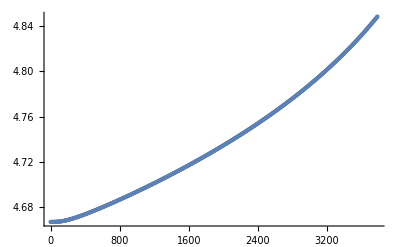

4.6667

4.68113

```mathematica
(*Volume vs temperature*)
ListPlot[normal[[3]]];
(*alatt vs temperature*)
ListPlot[Transpose@{Transpose[normal[[3]]][[1]],(Transpose[normal[[3]]][[2]])^(1/3)/2}]
VtoT=Interpolation[Transpose@{Transpose[normal[[3]]][[1]],(Transpose[normal[[3]]][[2]])^(1/3)/2}];
VtoTd=Interpolation[Transpose@{Transpose[defect[[3]]][[1]],(Transpose[defect[[3]]][[2]])^(1/3)/2}];
VtoT[4.7]
VtoTd[4.7]
```

```mathematica
Ttoalattpoly=Fit[Transpose@{Transpose[normal[[3]]][[1]],(Transpose[normal[[3]]][[2]])^(1/3)/2},{1,x,x*x,x*x*x,x*x*x*x},x]
```

4.66498+0.0000169781 x+1.50486×10^-8 x^2-4.52313×10^-12 x^3+7.26523×10^-16 x^4

```mathematica
Ttoalattpoly/.x->4000
```

4.87018

```mathematica
unitcellVtoTpoly=Fit[Transpose@{((Transpose[normal[[3]]][[2]])/8),Transpose[normal[[3]]][[1]]},{1,x,x*x,x*x*x,x*x*x*x},x];
atoTpoly=Fit[Transpose@{((Transpose[normal[[3]]][[2]])^(1/3)/2),Transpose[normal[[3]]][[1]]},{1,x,x*x,x*x*x,x*x*x*x},x];
TtoUnitcellpoly=Fit[Transpose@{Transpose[normal[[3]]][[1]],((Transpose[normal[[3]]][[2]])/8)},{1,x,x*x,x*x*x,x*x*x*x},x];
Table[unitcellVtoTpoly/.x->90+5i,{i,0,5}];
aToT[a_]:=(unitcellVtoTpoly)/.x->a;

unitcellVtoTpolyd=Fit[Transpose@{((Transpose[defect[[3]]][[2]])/8),Transpose[defect[[3]]][[1]]},{1,x,x*x,x*x*x,x*x*x*x},x];
aToTd[a_]:=(unitcellVtoTpolyd)/.x->a
```

```mathematica
TtoUnitcellpoly/.x->1000
```

103.374

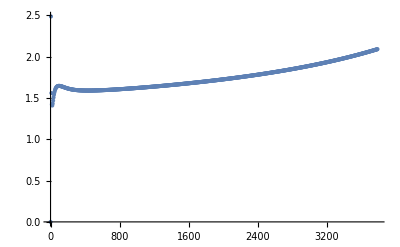

```mathematica
ListPlot@normal[[4]]
```

Show::gcomb: Could not combine the graphics objects in Show[dosAnalysisSixGruneisen,].

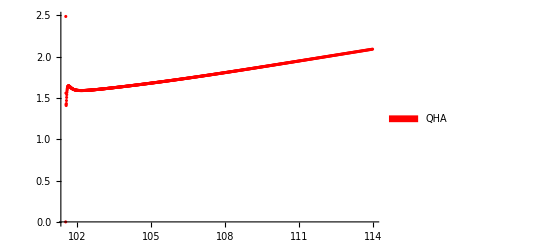
Show[dosAnalysisSixGruneisen,-Graphics-]

```mathematica
Show[dosAnalysisSixGruneisen,ListPlot[Transpose@{TtoUnitcellpoly/.x->Transpose[normal[[4]]][[1]],Transpose[normal[[4]]][[2]]},PlotStyle->Red,PlotLegends->SwatchLegend[{"QHA"}]]]
```

-1.29731×10^7+466969. x-6316.62 x^2+38.0451 x^3-0.0860437 x^4

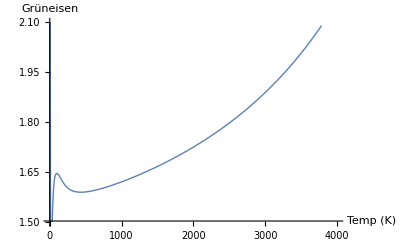

```mathematica
unitcellVtoTpolyd
c=ListPlot[normal[[4]],PlotRange->{{0,4000},{1.5,2.1}},Evaluate@swatch,AxesLabel->{"Temp\n(K)","Grüneisen"}]
```

```mathematica
unitcellVtoTpolyd
```

-1.29731×10^7+466969. x-6316.62 x^2+38.0451 x^3-0.0860437 x^4

```mathematica
aToTd[114]
```

3701.37

```mathematica
(*Convert temps to vols for prefect crystal*)
{{"300K:","760K:","1900K:","2500K:","3200K:","3805K:"},
{VtoT[300],VtoT[760],VtoT[1900],VtoT[2500],VtoT[3200],VtoT[3805]}}//TableForm
(*Convert temps to vols for prefect crystal*)
{{"4.625Ang","4.6583Ang:","4.685","4.6911exp:","4.730Ang:","4.759Ang:","4.801Ang:","4.850Ang"},
{aToT[4.625^3],aToT[4.6583^3],aToT[4.685^3],aToT[4.69106^3],aToT[4.730^3],aToT[4.759^3],aToT[4.801^3],aToT[4.850^3]}}//TableForm
```

InterpolatingFunction::dmval: Input value {3805} lies outside the range of data in the interpolating function. Extrapolation will be used.

300K: | 760K: | 1900K: | 2500K: | 3200K: | 3805K:
4.67072 | 4.685 | 4.72986 | 4.75913 | 4.80149 | 4.8505

4.625Ang | 4.6583Ang: | 4.685 | 4.6911exp: | 4.730Ang: | 4.759Ang: | 4.801Ang: | 4.850Ang
-1807.48 | -198.451 | 747.571 | 930.473 | 1909.15 | 2489.71 | 3195.7 | 3772.38

```mathematica
(*perefect QHA conductivity*)
qha4850={0.00003, 3760.0000 ,0.38039485, 0.39345184E+03, 0.43817897E-05 ,0.27853682E+21, 0.71474053E-10, 0.38557527E+17, 0.22661725E+03, 0.58738988E-08}
qha4801={}
```

{0.00003,3760.,0.380395,4.06951,-3.80891,21.7571,-8.05713,18.0481,3.61601,-6.40331}

{}

```mathematica
(*Convert temps to vols for defect crystal*)
{{"300K:","760K:","1900K:","2500K:","3200K:","3805K:"},
{VtoTd[300],VtoTd[760],VtoTd[1900],VtoTd[2500],VtoTd[3200],VtoTd[3805]}}//TableForm
(*Convert temps to vols for defect crystal*)
{{"4.625Ang","4.6583Ang:","4.685","4.6911exp:","4.730Ang:","4.759Ang:","4.801Ang:","4.850Ang"},
{aToTd[4.625^3],aToTd[4.6583^3],aToTd[4.685^3],aToTd[4.69106^3],aToTd[4.730^3],aToTd[4.759^3],aToTd[4.801^3],aToTd[4.850^3]}}//TableForm
```

300K: | 760K: | 1900K: | 2500K: | 3200K: | 3805K:
4.68529 | 4.69972 | 4.74455 | 4.77325 | 4.81362 | 4.85797

4.625Ang | 4.6583Ang: | 4.685 | 4.6911exp: | 4.730Ang: | 4.759Ang: | 4.801Ang: | 4.850Ang
-2584.97 | -802.005 | 263.187 | 469.912 | 1571.39 | 2213.51 | 2990.98 | 3715.94

```mathematica
qhad4850={0.00003, 3760.0000 ,0.38039485, 0.39345184E+03, 0.43817897E-05 ,0.27853682E+21, 0.71474053E-10, 0.38557527E+17, 0.22661725E+03, 0.58738988E-08}
```

{0.00003,3760.,0.380395,4.06951,-3.80891,21.7571,-8.05713,18.0481,3.61601,-6.40331}

```mathematica
(*Conductivity*)
condlabels={"Ef[Ry]"," T[K]"," N"," DOS(Ef)"," S"," s/t"," R_H"," kappa0 ","c ","chi"}
SetDirectory["/Volumes/MicroSD/PostDoc_SD/ZrC/Conductivity/RESULTS_qha"];

qhaCondfiles={"qha_all","qhad_all"};
perfectCondfiles={"4.6583exp_SPperf","4.685exp_SPperf","4.69106exp_SPperf","4.730exp_SPperf","4.759exp_SPperf","4.801exp_SPperf","4.850exp_SPperf"};

(*Note "4.759exp_SP" is exluded because something wrong with file - recheck conductivity calculation later*)
defectCondfiles={"4.685exp_SP","4.69106exp_SP","4.730exp_SP","4.801exp_SP","4.850exp_SP"};


qhaCondAll=Table[ReadList[qhaCondfiles[[i]],{Number, Number,Number,Number,Number,Number,Number,Number,Number,Number}],{i,1,2}];
perfectCondAll=Table[ReadList[perfectCondfiles[[i]],{Number, Number,Number,Number,Number,Number,Number,Number,Number,Number}],{i,1,7}];
defectCondAll=Table[ReadList[defectCondfiles[[i]],{Number, Number,Number,Number,Number,Number,Number,Number,Number,Number}],{i,1,5}];
```

{Ef[Ry], T[K], N, DOS(Ef), S, s/t, R_H, kappa0 ,c ,chi}

```mathematica
qhaCondAll[[1]]//TableForm;
perfectCondAll[[1]]//TableForm;
defectCondAll[[1]]//TableForm;
```

1.9746×10^-16

1.99455×10^-16

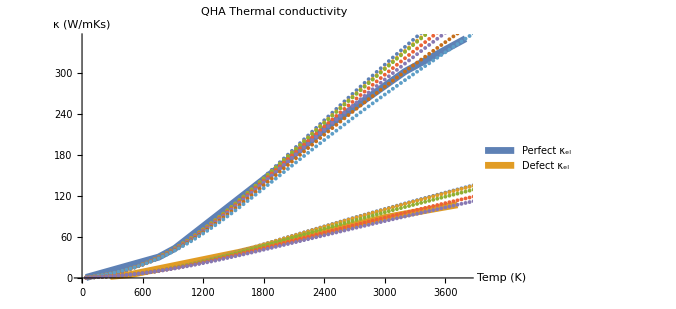

```mathematica
(*Electron Thermal Conductivity*)

(*RTA - relaxation time approximation*)
(*9*10^-14 - http://journals.aps.org/prb/pdf/10.1103/PhysRevB.12.1105*)
(* 0.3 eV = 0.3/(6.582*10^-16) = 4.55*10^-16 - plasma frequency - http://journals.aps.org/prb/pdf/10.1103/PhysRevB.32.7743*)
(*L=kappa/sigma*T=pi^2*kB^2/3e^2 = 2.45WOhm/K^2*)
tau=9*10^-15;
tau1=0.3*6.582*10^-16
1/(3.3/(6.582*10^-16))

condInfo1={AxesLabel->{"Temp (K)","κ (W/mKs)"},PlotLabel->"QHA Thermal conductivity",PlotLegends->SwatchLegend[{"Perfect κ_el","Defect κ_el"}],PlotStyle->Thickness[0.01]};

a1=ListPlot[Table[Transpose@{Transpose[qhaCondAll[[i]]][[2]],Transpose[tau*qhaCondAll[[i]]][[8]]},{i,1,2}],Evaluate@condInfo1,Joined->True];

b1=ListPlot[Table[Transpose@{Transpose[perfectCondAll[[i]]][[2]],Transpose[tau*perfectCondAll[[i]]][[8]]},{i,1,7}]];
c1=ListPlot[Table[Transpose@{Transpose[defectCondAll[[i]]][[2]],Transpose[tau*defectCondAll[[i]]][[8]]},{i,1,5}]];
Show[a1,b1,c1,ImageSize->500]
```

InterpolatingFunction::dmval: Input value {1.08169} lies outside the range of data in the interpolating function. Extrapolation will be used.

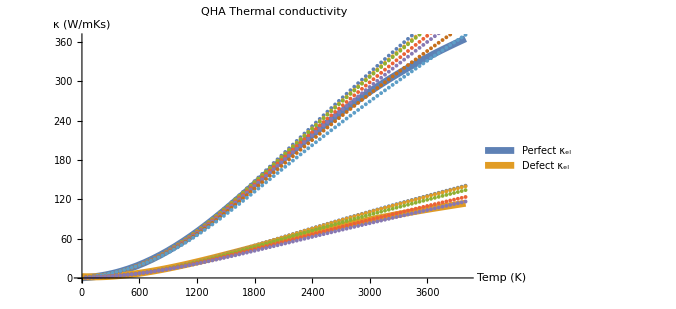

```mathematica
a1i=Plot[Evaluate@Table[Interpolation[Transpose@{Transpose[qhaCondAll[[i]]][[2]],tau*Transpose[qhaCondAll[[i]]][[8]]},InterpolationOrder->4][x],{i,1,2}],{x,1,4000},Evaluate@condInfo1];
b1i=Table[Interpolation[Transpose@{Transpose[perfectCondAll[[i]]][[2]],tau*Transpose[perfectCondAll[[i]]][[8]]}][x],{i,1,7}];
c1i=Table[Interpolation[Transpose@{Transpose[defectCondAll[[i]]][[2]],tau*Transpose[defectCondAll[[i]]][[8]]}][x],{i,1,5}];
Show[a1i,b1,c1,ImageSize->500]
```

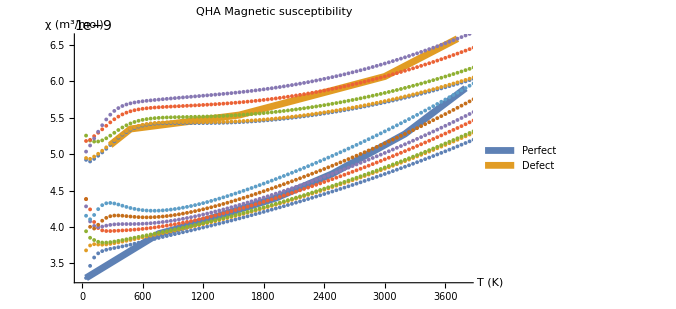

```mathematica
(*Electron Magnetic susceptibility*)
condInfo2={AxesLabel->{"T (K)","χ (m^3/mol)"},PlotLabel->"QHA Magnetic susceptibility",PlotLegends->SwatchLegend[{"Perfect","Defect"}],PlotStyle->Thickness[0.01]};

a2=ListPlot[Table[Transpose@{Transpose[qhaCondAll[[i]]][[2]],Transpose[qhaCondAll[[i]]][[10]]},{i,1,2}],Evaluate@condInfo2,Joined->True];
b2=ListPlot[Table[Transpose@{Transpose[perfectCondAll[[i]]][[2]],Transpose[perfectCondAll[[i]]][[10]]},{i,1,7}]];
c2=ListPlot[Table[Transpose@{Transpose[defectCondAll[[i]]][[2]],Transpose[defectCondAll[[i]]][[10]]},{i,1,5}]];
Show[a2,b2,c2,ImageSize->500]
```

InterpolatingFunction::dmval: Input value {1.08169} lies outside the range of data in the interpolating function. Extrapolation will be used.

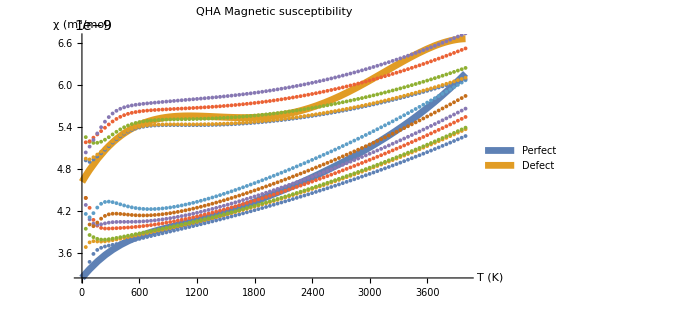

```mathematica
a2i=Plot[Evaluate@Table[Interpolation[Transpose@{Transpose[qhaCondAll[[i]]][[2]],Transpose[qhaCondAll[[i]]][[10]]},InterpolationOrder->4][x],{i,1,2}],{x,1,4000},Evaluate@condInfo2];
b2i=Table[Interpolation[Transpose@{Transpose[perfectCondAll[[i]]][[2]],Transpose[perfectCondAll[[i]]][[10]]}][x],{i,1,7}];
c2i=Table[Interpolation[Transpose@{Transpose[defectCondAll[[i]]][[2]],Transpose[defectCondAll[[i]]][[10]]}][x],{i,1,5}];
Show[a2i,b2,c2,ImageSize->500]
```

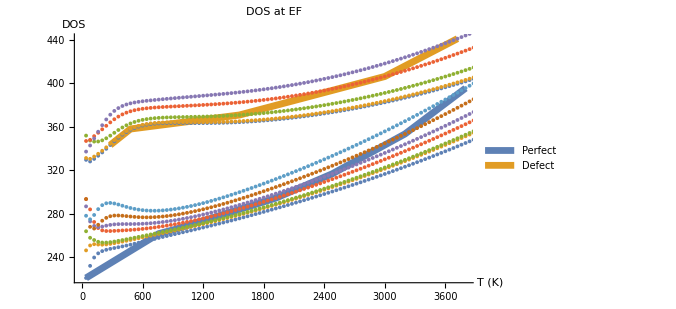

```mathematica
(*DOS *)
condInfo3={AxesLabel->{"T (K)","DOS"},PlotLabel->"DOS at EF",PlotLegends->SwatchLegend[{"Perfect","Defect"}],PlotStyle->Thickness[0.01]};

a3=ListPlot[Table[Transpose@{Transpose[qhaCondAll[[i]]][[2]],Transpose[qhaCondAll[[i]]][[4]]},{i,1,2}],Evaluate@condInfo3,Joined->True];
b3=ListPlot[Table[Transpose@{Transpose[perfectCondAll[[i]]][[2]],Transpose[perfectCondAll[[i]]][[4]]},{i,1,7}]];
c3=ListPlot[Table[Transpose@{Transpose[defectCondAll[[i]]][[2]],Transpose[defectCondAll[[i]]][[4]]},{i,1,5}]];
Show[a3,b3,c3,ImageSize->500]
```

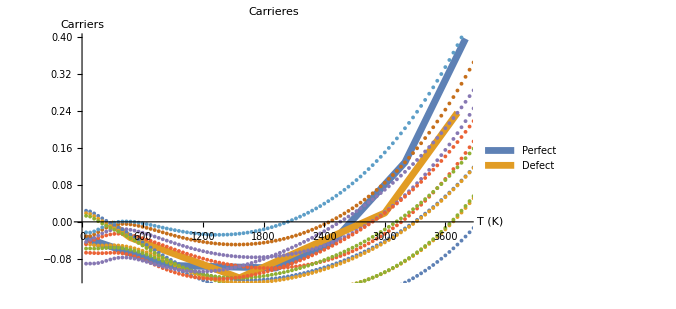

```mathematica
(*Carriers*)
condInfo4={AxesLabel->{"T (K)","Carriers"},PlotLabel->"Carrieres",PlotLegends->SwatchLegend[{"Perfect","Defect"}],PlotStyle->Thickness[0.01]};

a4=ListPlot[Table[Transpose@{Transpose[qhaCondAll[[i]]][[2]],Transpose[qhaCondAll[[i]]][[3]]},{i,1,2}],Evaluate@condInfo4,Joined->True];
b4=ListPlot[Table[Transpose@{Transpose[perfectCondAll[[i]]][[2]],Transpose[perfectCondAll[[i]]][[3]]},{i,1,7}]];
c4=ListPlot[Table[Transpose@{Transpose[defectCondAll[[i]]][[2]],Transpose[defectCondAll[[i]]][[3]]},{i,1,5}]];
Show[a4,b4,c4,ImageSize->500]
```

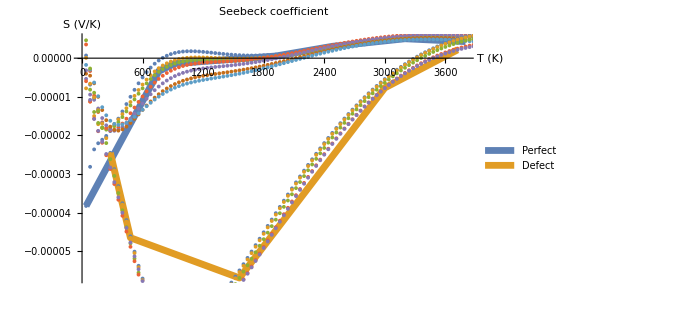

```mathematica
(*Seebeck*)
condInfo5={AxesLabel->{"T (K)","S (V/K)"},PlotLabel->"Seebeck coefficient",PlotLegends->SwatchLegend[{"Perfect","Defect"}],PlotStyle->Thickness[0.01]};

a5=ListPlot[Table[Transpose@{Transpose[qhaCondAll[[i]]][[2]],Transpose[qhaCondAll[[i]]][[5]]},{i,1,2}],Evaluate@condInfo5,Joined->True];
b5=ListPlot[Table[Transpose@{Transpose[perfectCondAll[[i]]][[2]],Transpose[perfectCondAll[[i]]][[5]]},{i,1,7}]];
c5=ListPlot[Table[Transpose@{Transpose[defectCondAll[[i]]][[2]],Transpose[defectCondAll[[i]]][[5]]},{i,1,5}]];
Show[a5,b5,c5,ImageSize->500]
```

```mathematica
(*Conductivity electrical*)
condInfo6={AxesLabel->{"T (K)","σ (1/Ωm)"},PlotLabel->"Charge conductivity",PlotLegends->SwatchLegend[{"Perfect","Defect"}],PlotStyle->Thickness[0.01]};

a6=ListPlot[Table[Transpose@{Transpose[qhaCondAll[[i]]][[2]],Transpose[qhaCondAll[[i]]][[6]]},{i,1,2}],Evaluate@condInfo6,Joined->True];
b6=ListPlot[Table[Transpose@{Transpose[perfectCondAll[[i]]][[2]],Transpose[perfectCondAll[[i]]][[6]]},{i,1,7}]];
c6=ListPlot[Table[Transpose@{Transpose[defectCondAll[[i]]][[2]],Transpose[defectCondAll[[i]]][[6]]},{i,1,5}]];
Show[a6,b6,c6,ImageSize->500]
```

-Graphics-

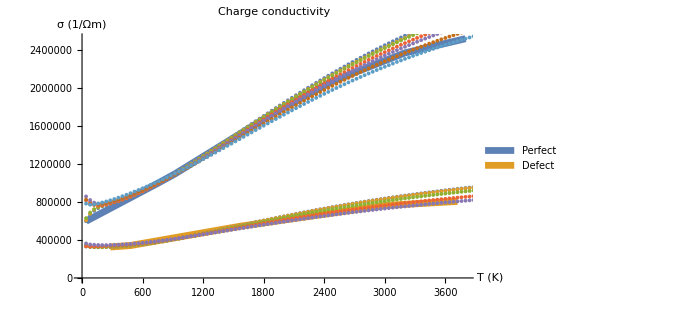

```mathematica
(*Conductivity electrical*)
condInfo6={AxesLabel->{"T (K)","σ (1/Ωm)"},PlotLabel->"Charge conductivity",PlotLegends->SwatchLegend[{"Perfect","Defect"}],PlotStyle->Thickness[0.01]};

a6=ListPlot[Table[Transpose@{Transpose[qhaCondAll[[i]]][[2]],tau*Transpose[qhaCondAll[[i]]][[6]]},{i,1,2}],Evaluate@condInfo6,Joined->True];
b6=ListPlot[Table[Transpose@{Transpose[perfectCondAll[[i]]][[2]],tau*Transpose[perfectCondAll[[i]]][[6]]},{i,1,7}]];
c6=ListPlot[Table[Transpose@{Transpose[defectCondAll[[i]]][[2]],tau*Transpose[defectCondAll[[i]]][[6]]},{i,1,5}]];
Show[a6,b6,c6,ImageSize->500]
(*exp 4.3*10^-7*)
```

```mathematica
1/(4.3*10^-7)
```

2.32558×10^6

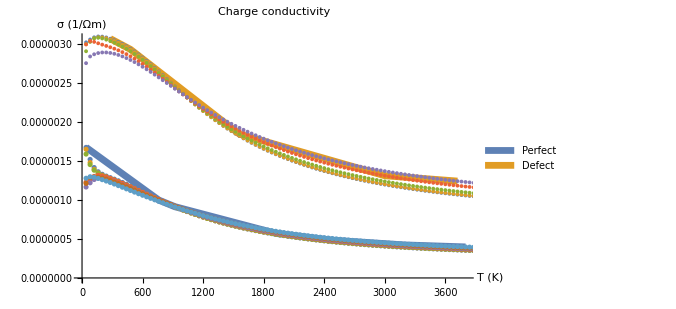

```mathematica
(*Conductivity electrical*)
condInfo6={AxesLabel->{"T (K)","σ (1/Ωm)"},PlotLabel->"Charge conductivity",PlotLegends->SwatchLegend[{"Perfect","Defect"}],PlotStyle->Thickness[0.01]};

a6=ListPlot[Table[Transpose@{Transpose[qhaCondAll[[i]]][[2]],1/(tau*Transpose[qhaCondAll[[i]]][[6]])},{i,1,2}],Evaluate@condInfo6,Joined->True];
b6=ListPlot[Table[Transpose@{Transpose[perfectCondAll[[i]]][[2]],1/(tau*Transpose[perfectCondAll[[i]]][[6]])},{i,1,7}]];
c6=ListPlot[Table[Transpose@{Transpose[defectCondAll[[i]]][[2]],1/(tau*Transpose[defectCondAll[[i]]][[6]])},{i,1,5}]];
Show[a6,b6,c6,ImageSize->500]
```

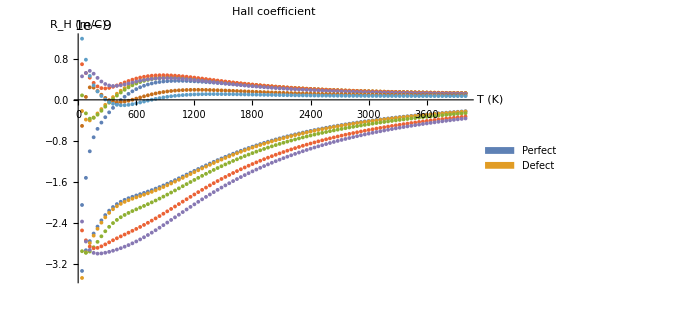

```mathematica
(*Hall coefficient*)
condInfo7={AxesLabel->{"T (K)","R_H (m/C)"},PlotLabel->"Hall coefficient",PlotLegends->SwatchLegend[{"Perfect","Defect"}],PlotStyle->Thickness[0.01]};

a7=ListPlot[Table[Transpose@{Transpose[qhaCondAll[[i]]][[2]],Transpose[qhaCondAll[[i]]][[7]]},{i,1,2}],Evaluate@condInfo7,Joined->True];
b7=ListPlot[Table[Transpose@{Transpose[perfectCondAll[[i]]][[2]],Transpose[perfectCondAll[[i]]][[7]]},{i,1,7}],AxesLabel->{"T (K)","R_H (m/C)"},PlotLabel->"Hall coefficient",PlotLegends->SwatchLegend[{"Perfect","Defect"}]];
c7=ListPlot[Table[Transpose@{Transpose[defectCondAll[[i]]][[2]],Transpose[defectCondAll[[i]]][[7]]},{i,1,5}]];
Show[b7,c7,ImageSize->500,PlotRange->All]
```

```mathematica
(*Phonopy lattice conductivity*)
SetDirectory["/Volumes/MicroSD/PostDoc_SD/ZrC/Conductivity/Results_phono3py_ZrC"];
filePhonopy={"t_kappa_4685","t_kappa_4691","t_kappa_4730"};
filePhonopyAll=Table[ReadList[filePhonopy[[i]],{Number, Number,Number, Number,Number, Number,Number}],{i,1,3}];
```

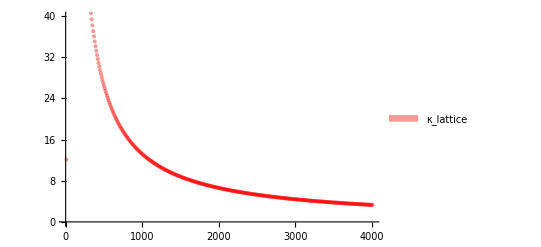

```mathematica
a8=ListPlot[Transpose@{Transpose[filePhonopyAll[[2]]][[1]],Transpose[filePhonopyAll[[2]]][[4]]},PlotStyle->{Red,Opacity[0.4]},PlotLegends->SwatchLegend[{"κ_lattice"}]]
```

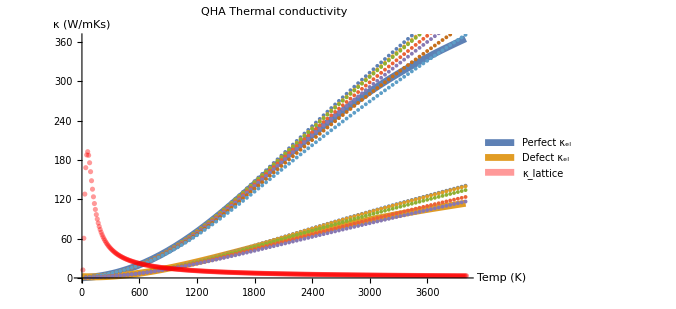

```mathematica
Show[a1i,b1,c1,a8,ImageSize->500]
```

```mathematica
condInfo1={PlotRange->{{0,2700},{0,70}},AxesLabel->{"Temp (K)","κ (W/mKs)"},PlotLabel->"QHA Thermal conductivity",PlotLegends->SwatchLegend[{"Perfect κ_el","Defect κ_el"}],PlotStyle->Thickness[0.01]};

a1i=Plot[Evaluate@Table[Interpolation[Transpose@{Transpose[qhaCondAll[[i]]][[2]],tau*Transpose[qhaCondAll[[i]]][[8]]},InterpolationOrder->4][x],{i,1,2}],{x,1,4000},Evaluate@condInfo1];


b1=ListPlot[Table[Transpose@{Transpose[perfectCondAll[[i]]][[2]],Transpose[tau*perfectCondAll[[i]]][[8]]},{i,1,7}]];
c1=ListPlot[Table[Transpose@{Transpose[defectCondAll[[i]]][[2]],Transpose[tau*defectCondAll[[i]]][[8]]},{i,1,5}]];
```

InterpolatingFunction::dmval: Input value {1.08169} lies outside the range of data in the interpolating function. Extrapolation will be used.

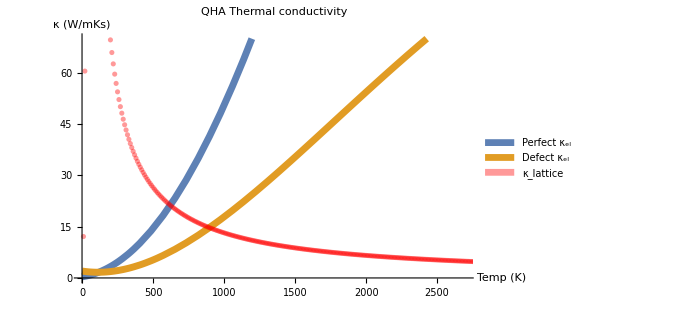

```mathematica
Show[a1i,a8,ImageSize->500]
```

```mathematica
(*Reduction in heat capcity at the melting point*)
defect[[7]][[376]]
defect[[7]][[375]]
normal[[7]][[750]]
(normal[[7]][[750]][[2]]-2170)/normal[[7]][[750]][[2]]*100
```

{3750.,2172.3038958851248}

{3740.,2167.24184181466717}

{3745.,2302.06035785898575}

5.7366157845577739

```mathematica
(*Franz-Wiedemnann law*)
(*L=constant=kappa_el/(sigma_el*T)*)
```

```mathematica
(*defect electron thermal conductivity*)
x1=Table[Interpolation[Transpose@{Transpose[defectCondAll[[i]]][[2]],tau*Transpose[defectCondAll[[i]]][[8]]}][x],{i,1,5}];

(*Defect electron charge conductivity*)
x6=Table[Interpolation[Transpose@{Transpose[defectCondAll[[i]]][[2]],tau*Transpose[defectCondAll[[i]]][[6]]}][x],{i,1,5}];
```

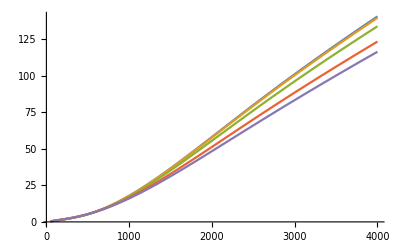

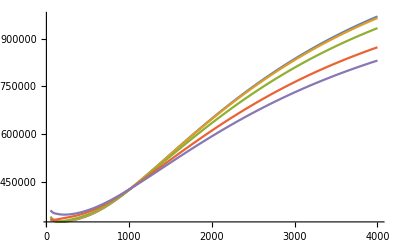

```mathematica
(*defect electron thermal conductivity*)
Plot[Evaluate@Table[Interpolation[Transpose@{Transpose[defectCondAll[[i]]][[2]],tau*Transpose[defectCondAll[[i]]][[8]]}][x],{i,1,5}],{x,50,4000}]

(*Defect electron charge conductivity*)
Plot[Evaluate@Table[Interpolation[Transpose@{Transpose[defectCondAll[[i]]][[2]],tau*Transpose[defectCondAll[[i]]][[6]]}][x],{i,1,5}],{x,50,4000}]
```

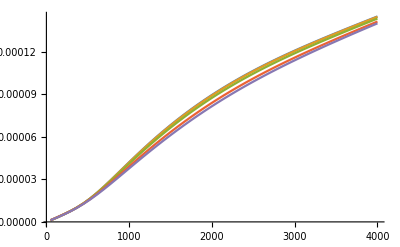

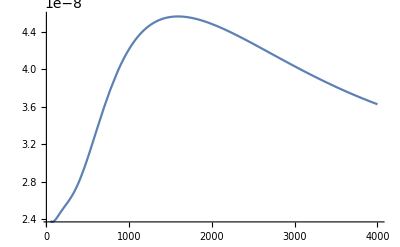

```mathematica
(*Defect kappa/(sigma*T)*)
Plot[Evaluate@Table[Interpolation[Transpose@{Transpose[defectCondAll[[i]]][[2]],(tau*Transpose[defectCondAll[[i]]][[8]])/(tau*Transpose[defectCondAll[[i]]][[6]])}][x],{i,1,5}],{x,50,4000}]
(*Defect kappa/(sigma*T) = Lorentz number*)
Plot[Evaluate@Table[Interpolation[Transpose@{Transpose[defectCondAll[[i]]][[2]],(tau*Transpose[defectCondAll[[i]]][[8]])/(x*tau*Transpose[defectCondAll[[i]]][[6]])}][x],{i,1,1}],{x,50,4000}]
(*Experimental Lorentz number s 2.44*10^-8 W Ohms K-^2*)
```

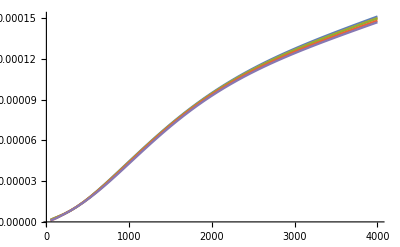

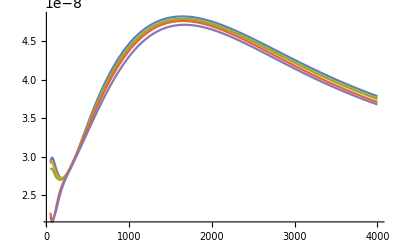

```mathematica
(*Perfect kappa/(sigma*T)*)
Plot[Evaluate@Table[Interpolation[Transpose@{Transpose[perfectCondAll[[i]]][[2]],(tau*Transpose[perfectCondAll[[i]]][[8]])/(tau*Transpose[perfectCondAll[[i]]][[6]])}][x],{i,1,5}],{x,50,4000}]
(*Perfect kappa/(sigma*T) = Lorentz number*)
Plot[Evaluate@Table[Interpolation[Transpose@{Transpose[perfectCondAll[[i]]][[2]],(tau*Transpose[perfectCondAll[[i]]][[8]])/(x*tau*Transpose[perfectCondAll[[i]]][[6]])}][x],{i,1,5}],{x,50,4000}]
(*Experimental Lorentz number s 2.44*10^-8 W Ohms K-^2*)
```